```mathematica
Quit[]
```

```mathematica
Clear[a,b,h,k,f,g,n,m];
a=0;b=1+2/6;c=0;d=1;m=8;n=5;
h=(b-a)/m;
k=(d-c)/n;
p=3;  
f[x_]:=0;
g[x_]:=0;
```

Definimos r para hacer mas comodamente la definición de las ecuaciones.

```mathematica
Clear[r]; 
r=p*k/h
```

18/5

```mathematica
h
```

1/6

Nodos:

Mostramos los nodos en ambos ejes:

```mathematica
Print["Los nodos del eje X son:  ",ptX=Table[Subscript[x, i]=a+i*h,{i,0,m}]];
Print["Los nodos del eje Y son:  ",ptY=Table[Subscript[t, j]=c+j*k,{j,0,n}]];
```

Los nodos del eje X son:  {0,1/6,1/3,1/2,2/3,5/6,1,7/6,4/3}

Los nodos del eje Y son:  {0,1/5,2/5,3/5,4/5,1}

Presentamos en una lista y en un gráfico los puntos de la malla resultante:

```mathematica
Clear[Nod,Nodos];
Nod=Table[{Subscript[x, i],Subscript[t, j]},{j,0,n},{i,0,m}];
Nodos=Flatten[Nod,1];
If[(n-2)(n-2)≤800,Print["Y los puntos de la malla serían (ordenados lexicográficamente) :  ",Nodos]];
```

Y los puntos de la malla serían (ordenados lexicográficamente) :  {{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0},{7/6,0},{4/3,0},{0,1/5},{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5},{1,1/5},{7/6,1/5},{4/3,1/5},{0,2/5},{1/6,2/5},{1/3,2/5},{1/2,2/5},{2/3,2/5},{5/6,2/5},{1,2/5},{7/6,2/5},{4/3,2/5},{0,3/5},{1/6,3/5},{1/3,3/5},{1/2,3/5},{2/3,3/5},{5/6,3/5},{1,3/5},{7/6,3/5},{4/3,3/5},{0,4/5},{1/6,4/5},{1/3,4/5},{1/2,4/5},{2/3,4/5},{5/6,4/5},{1,4/5},{7/6,4/5},{4/3,4/5},{0,1},{1/6,1},{1/3,1},{1/2,1},{2/3,1},{5/6,1},{1,1},{7/6,1},{4/3,1}}

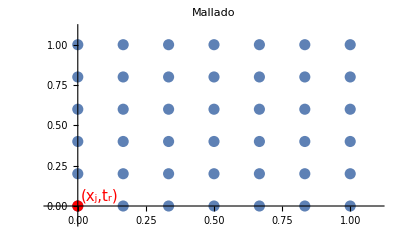

```mathematica
If[(n-2)(n-2)≤800,ListPlot[Nodos,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotStyle->PointSize[0.02],PlotLabel->"Mallado",FrameLabel->{"Eje t","Eje x"},Epilog->{Red,PointSize[0.02],Point[{0,0}],Text[Style["(x_j,t_r)",FontSize->15],Offset[{0,0},{0.08,0.06}]]}]]
```

```mathematica
h
```

1/6

```mathematica
Puntos=Table[{Subscript[x, i],Subscript[t, j]},{i,2,4},{j,2,2}];
PuntosNegros=Append[Flatten[Puntos,1],{Subscript[x, 3],Subscript[t, 1]}];
```

```mathematica
Print[PuntosNegros]
```

{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}

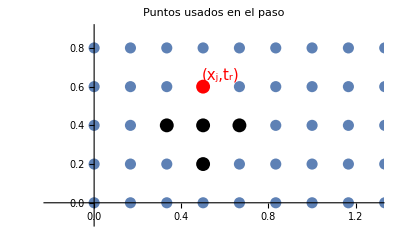

```mathematica
If[(n-2)(n-2)≤800,ListPlot[{Nodos, PuntosNegros},PlotRange->{{-0.2,1.3},{-0.1,0.9}},PlotStyle->{{PointSize[0.02]},{PointSize[0.025],Black}},PlotLabel->"Puntos usados en el paso",FrameLabel->{"Eje t","Eje x"},Epilog->{Red,PointSize[0.025],Point[{0.5,0.6}],Text[Style["(x_j,t_r)",FontSize->15],Offset[{0,0},{0.58,0.66}]]}   ]]
```

```mathematica
Clear[Puntos,PuntosNegros]
```

```mathematica
Puntos=Table[{Subscript[x, i],Subscript[t, j]},{j,0,3},{i,j,6-j}];
Print[Puntos]
```

{{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0}},{{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5}},{{1/3,2/5},{1/2,2/5},{2/3,2/5}},{{1/2,3/5}}}

{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0},{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5},{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,3/5}}

{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}

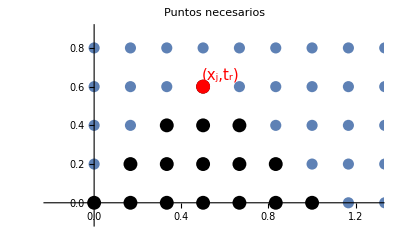

```mathematica
PuntosNegros=Flatten[Puntos,1];
Print[PuntosNegros]
{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}
If[(n-2)(n-2)≤800,ListPlot[{Nodos, PuntosNegros},PlotRange->{{-0.2,1.3},{-0.1,0.9}},PlotStyle->{{PointSize[0.02]},{PointSize[0.025],Black}},PlotLabel->"Puntos necesarios",FrameLabel->{"Eje t","Eje x"},Epilog->{Red,PointSize[0.025],Point[{0.5,0.6}],Text[Style["(x_j,t_r)",FontSize->15],Offset[{0,0},{0.58,0.66}]]}   ]]
```

```mathematica
Clear[Puntos,PuntosNegros]
```

```mathematica
Puntos=Table[{Subscript[x, i],Subscript[t, j]},{j,0,3},{i,j,6-j}];
Print[Puntos]
```

{{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0}},{{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5}},{{1/3,2/5},{1/2,2/5},{2/3,2/5}},{{1/2,3/5}}}

```mathematica
PuntosNegros=Flatten[Puntos,1];
Print[PuntosNegros]
{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}
```

{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0},{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5},{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,3/5}}

{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}

```mathematica
Punto1={0,0}
Punto2={0.85,0}
```

{0,0}

{0.85,0}

```mathematica
PuntosAzules={Punto1,Punto2}
```

{{0,0},{0.85,0}}

```mathematica
PuntosVerdes=Flatten[Table[{Subscript[x, i],Subscript[t, j]},{j,0,0},{i,0,6}],1]
```

{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0}}

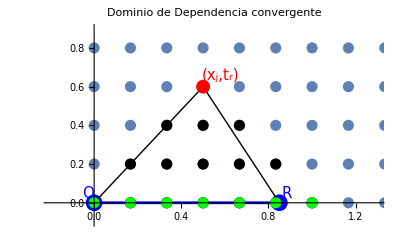

```mathematica
Show[ListPlot[{Nodos, PuntosNegros,PuntosAzules},PlotRange->{{-0.2,1.3},{-0.1,0.9}},PlotStyle->{{PointSize[0.02]},{PointSize[0.02],Black},{PointSize[0.03],Blue}},PlotLabel->"Dominio de Dependencia convergente",FrameLabel->{"Eje t","Eje x"},Epilog->{Red,PointSize[0.025],Point[{0.5,0.6}],Text[Style["(x_j,t_r)",FontSize->15],Offset[{0,0},{0.58,0.66}]]}   ], Graphics[{Line[{Punto1,{0.5,0.6}}],Text[Style["Q",Blue,FontSize->15],Offset[Punto1,Punto1+{-0.03,0.05}]]}],Graphics[{Line[{{0.5,0.6},Punto2}],Text[Style["R",Blue,FontSize->15],Offset[Punto2,Punto2+{0.03,0.05}]]},Axes->True,AspectRatio->1],Graphics[{AbsoluteThickness[2], Blue,Line[{Punto1,Punto2}]},Axes->True,AspectRatio->1],ListPlot[{PuntosVerdes},PlotStyle->{{Green,PointSize[0.020]}}]]
```

```mathematica
Clear[Puntos,PuntosNegros]
```

```mathematica
Puntos=Table[{Subscript[x, i],Subscript[t, j]},{j,0,3},{i,j,6-j}];
Print[Puntos]
```

{{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0}},{{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5}},{{1/3,2/5},{1/2,2/5},{2/3,2/5}},{{1/2,3/5}}}

```mathematica
PuntosNegros=Flatten[Puntos,1];
Print[PuntosNegros]
{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}
```

{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0},{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5},{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,3/5}}

{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}

```mathematica
Punto1={-0.1,0}
Punto2={1.2,0}
```

{-0.1,0}

{1.2,0}

```mathematica
PuntosAzules={Punto1,Punto2}
```

{{-0.1,0},{1.2,0}}

```mathematica
PuntosVerdes=Flatten[Table[{Subscript[x, i],Subscript[t, j]},{j,0,0},{i,0,6}],1]
```

{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0}}

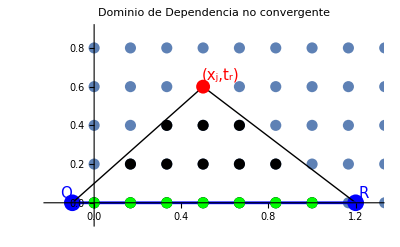

```mathematica
Show[ListPlot[{Nodos, PuntosNegros,PuntosAzules},PlotRange->{{-0.2,1.3},{-0.1,0.9}},PlotStyle->{{PointSize[0.02]},{PointSize[0.02],Black},{PointSize[0.03],Blue}},PlotLabel->"Dominio de Dependencia no convergente",FrameLabel->{"Eje t","Eje x"},Epilog->{Red,PointSize[0.025],Point[{0.5,0.6}],Text[Style["(x_j,t_r)",FontSize->15],Offset[{0,0},{0.58,0.66}]]}   ], Graphics[{Line[{Punto1,{0.5,0.6}}],Text[Style["Q",Blue,FontSize->15],Offset[Punto1,Punto1+{-0.03,0.05}]]}],Graphics[{Line[{{0.5,0.6},Punto2}],Text[Style["R",Blue,FontSize->15],Offset[Punto2,Punto2+{0.03,0.05}]]},Axes->True,AspectRatio->1],Graphics[{AbsoluteThickness[2], Blue,Line[{Punto1,Punto2}]},Axes->True,AspectRatio->1],ListPlot[{PuntosVerdes},PlotStyle->{{Green,PointSize[0.020]}}]]
```

```mathematica
Clear[Puntos,PuntosNegros]
```

```mathematica
Puntos=Table[{Subscript[x, i],Subscript[t, j]},{j,0,3},{i,j,6-j}];
Print[Puntos]
```

{{{0,0},{1/6,0},{1/3,0},{1/2,0},{2/3,0},{5/6,0},{1,0}},{{1/6,1/5},{1/3,1/5},{1/2,1/5},{2/3,1/5},{5/6,1/5}},{{1/3,2/5},{1/2,2/5},{2/3,2/5}},{{1/2,3/5}}}

```mathematica
PuntosNegros=Flatten[Puntos,1];
Print[PuntosNegros]
{{1/3,2/5},{1/2,2/5},{2/3,2/5},{1/2,1/5}}
If[(n-2)(n-2)≤800,ListPlot[{Nodos, PuntosNegros},PlotRange->{{-0.2,1.3},{-0.1,0.9}},PlotStyle->{{PointSize[0.02]},{PointSize[0.025],Black}},PlotLabel->"Puntos necesarios",FrameLabel->{"Eje t","Eje x"},Epilog->{Red,PointSize[0.025],Point[{0.5,0.6}],Text[Style["(x_j,t_r)",FontSize->15],Offset[{0,0},{0.58,0.66}]]}   ]]
```

```mathematica
Graphics[{Arrowheads[0.05],Arrow[{{0,0},{2,4}}]}]
```

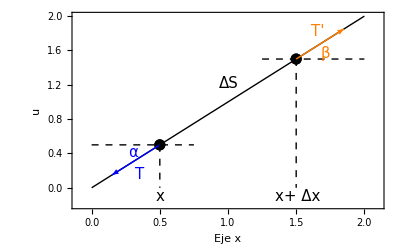

```mathematica
Show[ListPlot[{{{1.5,1.5}} ,{{0.5,0.5}}},PlotRange->{{-0.1,2.1},{-0.2,2}},PlotStyle->{{PointSize[0.02],Black},{PointSize[0.02],Black}},FrameLabel->{"Eje x","u"},Frame->{True,True,False,False}], Graphics[{Line[{{0,0},{2,2}}],Text[Style["α",Blue,FontSize->15],Offset[{0.5,0.5},{0.5,0.5}+{-0.2,-0.1}]]}],Graphics[{Blue,Arrowheads[0.05],Arrow[{{0.5,0.5},{0.15,0.15}}],Text[Style["T",Blue,FontSize->15],Offset[{0.5,0.5},{0.5,0.5}+{-0.15,-0.35}]]}],Graphics[{Dashed,Line[{{0,0.5},{0.75,0.5}}],Text[Style["β",Orange,FontSize->15],Offset[{1.5,1.5},{1.5,1.5}+{0.2,0.05}]]}],Graphics[{Dashed,Line[{{1.25,1.5},{2,1.5}}],Text[Style["ΔS",FontSize->15],Offset[{1,1},{1,1.2}]]}],Graphics[{Orange,Arrowheads[0.05],Arrow[{{1.5,1.5},{1.85,1.85}}],Text[Style["T'",Orange,FontSize->15],Offset[{1.5,1.5},{1.5,1.5}+{0.15,0.3}]]}],
Graphics[{Dashed,Line[{{0.5,0.5},{0.5,0}}],Text[Style["x",FontSize->15],Offset[{0.5,0},{0.5,0}+{0,-0.1}]]}],Graphics[{Dashed,Line[{{1.5,1.5},{1.5,0}}],Text[Style["x+ Δx",FontSize->15],Offset[{1.5,0},{1.5,0}+{0,-0.1}]]}]]
```